25

1.64646

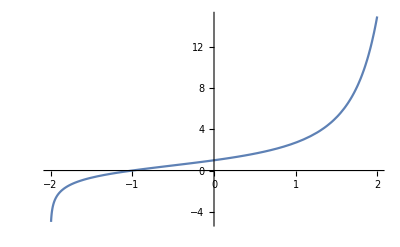

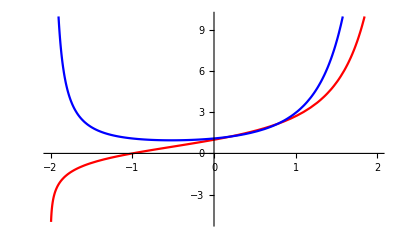

0.402706

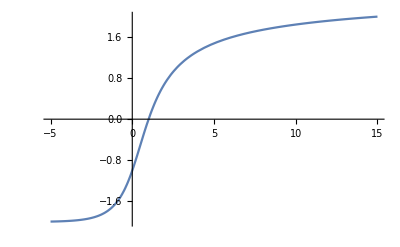

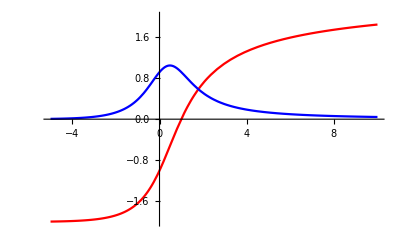

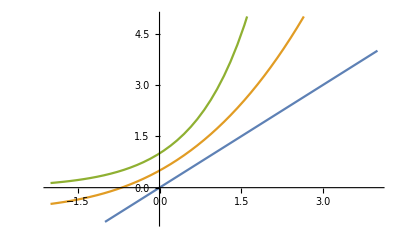

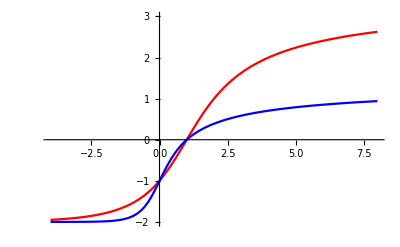

```mathematica
(*
**Usage:
**env=SuperLogPrepare[n,x];**SuperLog[env,z]-- gives n-th approx.of slog_x(z)**Tetrate[env,y]-- gives n-th approx.of x^^y**Copyright 2005 Andrew Robbins*)SuperLogPrepare[n_Integer,x_]:={x,LinearSolve[Table[k^j/k!-If[j==k,Log[x]^-k,0],{j,0,n-1},{k,1,n}],Table[If[k==1,1,0],{k,1,n}]]}
SuperLog[v_,z_?NumericQ]:=Block[{(*SlogCrit*)},SlogCrit[zc_]:=-1+Sum[v[[2,k]]*zc^k/k!,{k,1,Length[v[[2]]]}];
Which[z≤0,SlogCrit[v[[1]]^z]-1,0<z≤1,SlogCrit[z],z>1,Block[{i=-1},SlogCrit[NestWhile[Log[v[[1]],#]&,z,(i++;#>1)&]]+i]]]
Tetrate[v_,y_?NumericQ]:=Block[{(*SlogCrit,TetCrit*)},SlogCrit[zc_]:=-1+Sum[v[[2,k]]*zc^k/k!,{k,1,Length[v[[2]]]}];
TetCrit[yc_]:=FindRoot[SlogCrit[z]==yc,{z,1}][[1,2]];If[y>-1,Nest[Power[v[[1]],#]&,TetCrit[y-Ceiling[y]],Ceiling[y]],Nest[Log[v[[1]],#]&,TetCrit[y-Ceiling[y]],-Ceiling[y]]]]
(*Gives the k-th numerical derivative of f(x) at x=c:*)
ND[f_,x_,c_]:=ND[f,x,c,1]
ND[f_,x_,c_,k_]:=ND[f,x,c,k,0.0001]
ND[f_,x_,c_,0,h_]:=(f/.x->c)
ND[f_,x_,c_,k_,h_]/;k≠0:=(ND[f,x,c+h,k-1,h]-ND[f,x,c,k-1,h])/h
25
(***************************************)
(*A few commands to try for starters:*)
(***************************************)
(*Prepares the 10th approx.of slog_e(z):*)
(*the'=' is used here for immediate execution*)
(*the';' is used here to suppress display*)
env=SuperLogPrepare[10,E];
(*Shows e^^0.5,and plots of e^^y:*)
Tetrate[env,0.5]
Plot[Tetrate[env,y],{y,-2,2},PlotRange->{-5,15}]
Plot[{Tetrate[env,y],ND[Tetrate[env,t],t,y]},{y,-2,2},PlotRange->{-5,10},PlotStyle->{Hue[0],Hue[2/3]}]
(*Shows slog_e(1.5),and plots of slog_e(z):*)
SuperLog[env,1.5]
Plot[SuperLog[env,z],{z,-5,15},PlotRange->{-2,2}]
Plot[{SuperLog[env,z],ND[SuperLog[env,t],t,z]},{z,-5,10},PlotRange->{-2,2},PlotStyle->{Hue[0],Hue[2/3]}]
(*Shows the half-exponential function:*)
(*f(x) such that f(f(x))=exp(x)*)
HalfExp[x_]:=Tetrate[env,SuperLog[env,x]+1/2]
Plot[{x,HalfExp[x],HalfExp[HalfExp[x]]},{x,-2,4},PlotRange->{-1,5}]
(*Plots 5th approx.of slog at different bases:*)
Plot[{SuperLog[SuperLogPrepare[5,2],z],SuperLog[SuperLogPrepare[5,10],z]},{z,-4,8},PlotRange->{-2,3},PlotStyle->{Hue[0],Hue[2/3]}]
```